g2 graph 15 computation (level 2) DONE
Dependencies: ModCatFunctions (NCAlgebra)

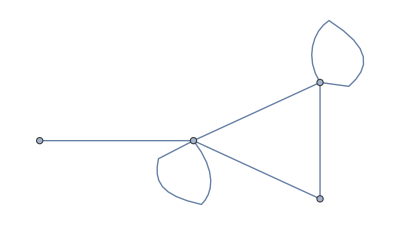

```mathematica
graph = { {0,1,0,0},{1,1,1,1},{0,1,1,1}, {0,1,1,0} };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo];
BGamma = { {0,aa,0,0},{bb,cc,dd,ee},{0,ff,gg,hh}, {0,ii,jj,0} };
q=Exp[2*Pi*I/36]; (* 2*Pi*I/(3*(4+ level)) *)
```

```mathematica
SetDirectory["/Users/calebhill/Documents/UNH/Research/code/gen2"];
Export["regularLowOrder_15.txt", regularLowOrderEqns//N];
```

```mathematica
(*Read the contents of the file*)
fileContent=Import["/Users/calebhill/Documents/UNH/Research/code/gen2/regularLowOrder_15.txt","Text"];

(*Replace "alpha1" with "alpha[1]"*)
For[ind=dim2to1,ind>=1,ind--,
	fileContent = StringReplace[fileContent,"alpha"<>ToString[ind]->"alpha["<>ToString[ind]<>"]"];
	Print["Replacing ", "alpha"<>ToString[ind], " with ", "alpha["<>ToString[ind]<>"]"]; 
]

(*Write the modified content back to the file*)
Export["/Users/calebhill/Documents/UNH/Research/code/gen2/regularLowOrder_15.txt",fileContent,"Text"];
```

```mathematica
q2 = 1/(q+q^(-1))//N
Sqrt[q2]
q3 = 1/(q^2+1+q^(-2))//N
Sqrt[q3]
```

0.507713+0. ⅈ

0.71254+0. ⅈ

0.347296+0. ⅈ

0.589319+0. ⅈ

Save the below work to recreate the methods later!

All equations:

```mathematica
linearSol = Solve[Join[lollipopEqns, rotateEqns]][[1]];
```

```mathematica
Eqs = Join[ bigonEqns, trigonEqns]/.linearSol//FullSimplify
```

{alpha4^2 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956==Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956,alpha4^2+alpha5^2+alpha20^2 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+((alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)^2)/((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^2)==1,alpha4^2 Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502==Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha5^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^2+alpha16^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^2+alpha14 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==Root2.06Root[-3-9 #1+3 #1^2+#1^3&,3]2.064177772475912,alpha20^2+alpha14 alpha21 Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689==1,alpha16^2+alpha17^2+Root0.742Root[1-3 #1+3 #1^3&,3]0.7422271989685592 (alpha17+alpha16 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)^2==1,alpha5^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^2+alpha16^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^2+alpha14 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==Root2.06Root[-3-9 #1+3 #1^2+#1^3&,3]2.064177772475912,alpha14 alpha21 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha17^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)==Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689,(-1+alpha20^2) Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184+alpha14 alpha21 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098==0,alpha14 alpha21 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha17^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)==Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689,alpha4 (alpha4 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)+Root-0.518Root[9-36 #1^2+9 #1^4+#1^6&,2]-0.5182380369166852)==0,alpha4 (alpha4 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)+Root-0.518Root[9-36 #1^2+9 #1^4+#1^6&,2]-0.5182380369166852)==0,(alpha20 Root-0.486Root[27-108 #1^2-27 #1^4+#1^6&,2]-0.48598053179093853+alpha5^3 Root1.38Root[1+36 #1^2-21 #1^4+#1^6&,3]1.3833052884485615+alpha5 Root-0.698Root[81-162 #1^2-9 #1^4+#1^6&,2]-0.6982202183332247+alpha20^3 Root0.847Root[3-9 #1^2+6 #1^4+#1^6&,4]0.8466885006553777+alpha4^3 Root2.20Root[-3-81 #1^2+12 #1^4+#1^6&,2]2.2011898968725703+alpha4 Root-0.439Root[-27+135 #1^2+27 #1^4+#1^6&,1]-0.43878618645957446) Root2.77Root[1-39 #1^2-18 #1^4+3 #1^6&,4]2.7723257768552902==(alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)^3,alpha4 (Root-0.574Root[-3-9 #1-6 #1^2+#1^3&,2]-0.5739779522395382+alpha4 (alpha4+alpha5 Root1.59Root[3-3 #1^4+#1^6&,4]1.5912538723402863+alpha20 Root1.11Root[1-6 #1^2+3 #1^4+#1^6&,4]1.1075565885794176))==0,alpha14 alpha20 alpha21 Root0.808Root[1-3 #1^4+#1^6&,3]0.8079007641202843+alpha5 (-alpha5^2+alpha16^2 Root0.879Root[-3+3 #1^2+#1^3&,3]0.8793852415718167+Root0.574Root[3-9 #1+6 #1^2+#1^3&,2]0.5739779522395382+alpha5 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212) Root-0.696Root[-1-3 #1^2+9 #1^4+3 #1^6&,1]-0.6960275841783272)==0,alpha14 alpha21 alpha5==(alpha20 (Root-0.879Root[3-3 #1^2+#1^3&,1]-0.8793852415718167+alpha20 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)))/((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)),alpha5 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184 (alpha5 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)+Root-0.825Root[-27+27 #1^2+18 #1^4+#1^6&,1]-0.8246482830377035)==alpha16^2 alpha5 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+alpha14 alpha20 alpha21 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098,alpha16 alpha5^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)+alpha14 alpha17 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==alpha16 Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606 (alpha16 (alpha17+alpha16 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)+Root-0.710Root[9-9 #1^2-18 #1^4+#1^6&,2]-0.7104560086219716),alpha21 (alpha20 alpha5 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha16 alpha17 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha14 alpha21 alpha5 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)==alpha20 (Root-0.879Root[3-3 #1^2+#1^3&,1]-0.8793852415718167+alpha20 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)),alpha14 (alpha20 alpha5 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha16 alpha17 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha5 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184 (alpha5 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)+Root-0.825Root[-27+27 #1^2+18 #1^4+#1^6&,1]-0.8246482830377035)==alpha16^2 alpha5 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+alpha14 alpha20 alpha21 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098,alpha16 alpha5^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)+alpha14 alpha17 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==alpha16 Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606 (alpha16 (alpha17+alpha16 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)+Root-0.710Root[9-9 #1^2-18 #1^4+#1^6&,2]-0.7104560086219716),alpha14 (alpha20 alpha5 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha16 alpha17 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha16 Root1.18Root[9-9 #1+#1^3&,2]1.1847925309040954+3 alpha16 alpha17^2 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha16^3 Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956+3 alpha16^2 alpha17 (Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)^3+alpha17 Root0.957Root[81-81 #1^2-9 #1^4+#1^6&,3]0.9571947910414242+alpha17^3 Root-1.01Root[1-57 #1^2+54 #1^4+#1^6&,1]-1.0090440624642514==0,alpha16 (alpha16^2+Root-0.574Root[-3-9 #1-6 #1^2+#1^3&,2]-0.5739779522395382+alpha5^2 Root-1.14Root[1-3 #1+3 #1^3&,1]-1.1371580426032577+alpha16 alpha17 Root0.808Root[1-3 #1^4+#1^6&,3]0.8079007641202843)+alpha14 alpha17 alpha21 Root-1.07Root[-1-3 #1^2+3 #1^6&,1]-1.0663761262346685==0,alpha14 alpha16 alpha21 Root1.07Root[-1-3 #1^2+3 #1^6&,2]1.0663761262346685==alpha17 (alpha17^2+Root-0.574Root[-3-9 #1-6 #1^2+#1^3&,2]-0.5739779522395382+alpha16 alpha17 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184),alpha21 (alpha20 alpha5 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha16 alpha17 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha14 alpha16 alpha21 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184==alpha17 (alpha17^2 Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689+alpha16 alpha17 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098+Root-0.666Root[27-81 #1^2+45 #1^4+#1^6&,2]-0.6662339779966412),alpha14 alpha21 alpha5 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)==alpha20 (Root-0.879Root[3-3 #1^2+#1^3&,1]-0.8793852415718167+alpha20 (alpha20+alpha4 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212+alpha5 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)),alpha21 (alpha20 alpha5 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha16 alpha17 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha14 (alpha16 alpha17 Root-1.35Root[-3+3 #1^2+#1^3&,2]-1.3472963553338606+Root-0.710Root[9-9 #1^2-18 #1^4+#1^6&,2]-0.7104560086219716+alpha20 alpha5 Root-1.32Root[1+6 #1^2-9 #1^4+3 #1^6&,1]-1.3199345434409084)==0,alpha14 alpha16 alpha21 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184==alpha17 (alpha17^2 Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689+alpha16 alpha17 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098+Root-0.666Root[27-81 #1^2+45 #1^4+#1^6&,2]-0.6662339779966412)}

```mathematica
Length[lollipopEqns]
Length[bigonEqns]
Length[trigonEqns]
Length[squareEqns]
Length[pentEqns]
```

```mathematica
sol = NSolve[Eqs, {alpha4, alpha5, alpha14, alpha16, alpha17, alpha20, alpha21}, Reals, 4]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(116690 alpha14)/183067+(169206 alpha16)/183067+(172209 alpha17)/183067-(151916 alpha20)/183067-(185189 alpha21)/183067-(117425 alpha4)/183067-(138285 alpha5)/183067 == 1.

{{alpha4→0.589,alpha5→-0.213,alpha14→-2.85,alpha16→-0.771,alpha17→0.508,alpha20→0.653,alpha21→-0.17},{alpha4→0.589,alpha5→-0.213,alpha14→-0.275,alpha16→-0.771,alpha17→0.508,alpha20→0.653,alpha21→-1.8},{alpha4→0.589,alpha5→-0.213,alpha14→-2.,alpha16→0.771,alpha17→-0.508,alpha20→0.653,alpha21→-0.25},{alpha4→0.589,alpha5→-0.213,alpha14→-0.393,alpha16→0.771,alpha17→-0.508,alpha20→0.653,alpha21→-1.26}}

```mathematica
0.5893185522438461324`3.//RootApproximant
```

1/18 (7+√13)

```mathematica
-0.2125731818910978058`3.6989700043360187//RootApproximant
```

1/16 (3-√41)

```mathematica
-0.7708945930629500376`3.6989700043360187//RootApproximant
```

Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481

```mathematica
0.6527075875256250463`3.6989700043360187//RootApproximant
```

Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393

```mathematica
Eqs/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325, alpha5->1/16 (3-√41), alpha16->Root"-0.771"Root[2+2 #1+#1^3&,1]-0.7709169970592481, alpha20->Root"0.653"Root[1-3 #1^2+#1^3&,2]0.6527036446661393}//Simplify
```

{Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956==Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 (Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325)^2,False,Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502==1,1/256 (-3+√41)^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^2+(Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^2+alpha14 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==Root2.06Root[-3-9 #1+3 #1^2+#1^3&,3]2.064177772475912,(Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393)^2+alpha14 alpha21 Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689==1,alpha17^2+(Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2+Root0.742Root[1-3 #1+3 #1^3&,3]0.7422271989685592 (alpha17+Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)^2==1,1/256 (-3+√41)^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^2+(Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^2+alpha14 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==Root2.06Root[-3-9 #1+3 #1^2+#1^3&,3]2.064177772475912,alpha14 alpha21 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha17^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)==Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689,(-1+(Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393)^2) Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184+alpha14 alpha21 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098==0,alpha14 alpha21 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956+alpha17^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)==Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689,False,False,False,False,alpha14 alpha21 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 Root0.808Root[1-3 #1^4+#1^6&,3]0.8079007641202843+1/16 (3-√41) (-1/256 (-3+√41)^2+(Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2 Root0.879Root[-3+3 #1^2+#1^3&,3]0.8793852415718167+Root0.574Root[3-9 #1+6 #1^2+#1^3&,2]0.5739779522395382-1/16 (-3+√41) (Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212) Root-0.696Root[-1-3 #1^2+9 #1^4+3 #1^6&,1]-0.6960275841783272)==0,-1/16 (-3+√41) alpha14 alpha21==(Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 (Root-0.879Root[3-3 #1^2+#1^3&,1]-0.8793852415718167+Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 (Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212-1/16 (-3+√41) Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)))/((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)),alpha14 alpha21 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098==1/16 ((-3+√41) (Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+(3-√41) Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184 (1/16 (3-√41) (Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212-1/16 (-3+√41) Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)+Root-0.825Root[-27+27 #1^2+18 #1^4+#1^6&,1]-0.8246482830377035)),1/256 (-3+√41)^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2) Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481+alpha14 alpha17 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606 (Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (alpha17+Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)+Root-0.710Root[9-9 #1^2-18 #1^4+#1^6&,2]-0.7104560086219716),alpha21 (-1/16 (-3+√41) Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,-1/16 (-3+√41) alpha14 alpha21 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)==Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 (Root-0.879Root[3-3 #1^2+#1^3&,1]-0.8793852415718167+Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 (Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212-1/16 (-3+√41) Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)),alpha14 (-1/16 (-3+√41) Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha14 alpha21 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098==1/16 ((-3+√41) (Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+(3-√41) Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184 (1/16 (3-√41) (Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212-1/16 (-3+√41) Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)+Root-0.825Root[-27+27 #1^2+18 #1^4+#1^6&,1]-0.8246482830377035)),1/256 (-3+√41)^2 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2) Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481+alpha14 alpha17 alpha21 Root1.78Root[3+27 #1^2-12 #1^4+#1^6&,3]1.7783429996571993==Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606 (Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (alpha17+Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)+Root-0.710Root[9-9 #1^2-18 #1^4+#1^6&,2]-0.7104560086219716),alpha14 (-1/16 (-3+√41) Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,Root1.18Root[9-9 #1+#1^3&,2]1.1847925309040954 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481+3 alpha17^2 Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481+(Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^3 Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956+3 alpha17 (Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2 (Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184)^3+alpha17 Root0.957Root[81-81 #1^2-9 #1^4+#1^6&,3]0.9571947910414242+alpha17^3 Root-1.01Root[1-57 #1^2+54 #1^4+#1^6&,1]-1.0090440624642514==0,Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 ((Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481)^2+Root-0.574Root[-3-9 #1-6 #1^2+#1^3&,2]-0.5739779522395382+1/256 (-3+√41)^2 Root-1.14Root[1-3 #1+3 #1^3&,1]-1.1371580426032577+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root0.808Root[1-3 #1^4+#1^6&,3]0.8079007641202843)+alpha14 alpha17 alpha21 Root-1.07Root[-1-3 #1^2+3 #1^6&,1]-1.0663761262346685==0,alpha14 alpha21 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.07Root[-1-3 #1^2+3 #1^6&,2]1.0663761262346685==alpha17 (alpha17^2+Root-0.574Root[-3-9 #1-6 #1^2+#1^3&,2]-0.5739779522395382+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184),alpha21 (-1/16 (-3+√41) Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha14 alpha21 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184==alpha17 (alpha17^2 Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098+Root-0.666Root[27-81 #1^2+45 #1^4+#1^6&,2]-0.6662339779966412),-1/16 (-3+√41) alpha14 alpha21 (Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)^(3/2)==Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 (Root-0.879Root[3-3 #1^2+#1^3&,1]-0.8793852415718167+Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 (Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325 Root0.903Root[1+3 #1^2-6 #1^4+#1^6&,3]0.9028884034563212-1/16 (-3+√41) Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098)),alpha21 (-1/16 (-3+√41) Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956 Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 (Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)^(3/2)+Root0.825Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035)==0,alpha14 (alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root-1.35Root[-3+3 #1^2+#1^3&,2]-1.3472963553338606+Root-0.710Root[9-9 #1^2-18 #1^4+#1^6&,2]-0.7104560086219716-1/16 (-3+√41) Root0.653Root[1-3 #1^2+#1^3&,2]0.6527036446661393 Root-1.32Root[1+6 #1^2-9 #1^4+3 #1^6&,1]-1.3199345434409084)==0,alpha14 alpha21 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.24Root[1-3 #1^2+#1^6&,4]1.23777578189184==alpha17 (alpha17^2 Root1.16Root[3-3 #1^4+#1^6&,3]1.1607309573427689+alpha17 Root-0.771Root[2+2 #1+#1^3&,1]-0.7709169970592481 Root1.44Root[-3-9 #1^2+3 #1^4+#1^6&,2]1.4367246682910098+Root-0.666Root[27-81 #1^2+45 #1^4+#1^6&,2]-0.6662339779966412)}

```mathematica
Eqs/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728/.alpha14->(Root"0.494"Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21/.alpha21->1/6 (-9-√33)/.{alpha16->Root"0.771"Root[{-3+21 #1^4+#1^6&,30+93 #1^2+8 #1^4-111 #2^2&},{2,2}]0.7708899366897215,alpha17->Root"-0.508"Root[{-3+21 #1^4+#1^6&,3-18 #2^2-3 #2^4+#2^6&,30+93 #1^2+8 #1^4-111 #3^2&,-21 #1^3 #2 #3-#1^5 #2 #3+3 #4&},{2,2,2,1}]-0.5077133059428725}//FullSimplify//TableForm
```

True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True
True

```mathematica
Solve[Eqs[[5]]/.alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728//FullSimplify,alpha14]//FullSimplify
```

{{alpha14→(Root0.494Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21}}

```mathematica
Solve[Eqs[[2]]/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}//FullSimplify, {alpha5},Reals]//FullSimplify
```

{{alpha5→Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728},{alpha5→Root0.490Root[-3-801 #1^2+3387 #1^4+#1^6&,2]0.4900648026593455}}

```mathematica
Solve[Eqs[[11]]/.alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325//FullSimplify, {alpha5,alpha20},Reals]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{alpha20→Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root0.205Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root-0.847Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}}

```mathematica
Solve[Eqs[[9]]/.alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502, {alpha14, alpha21}, Reals,3]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 alpha14)/87992-(121001 alpha21)/175984 == 1.

{{alpha14→0.66,alpha21→-2.5},{alpha14→-1.61,alpha21→1.}}

```mathematica
-2.4588907134076059604`2.6989700043360187//RootApproximant
```

1/6 (-9-√33)

```mathematica
Solve[{alpha16^2 Root"1.82"Root[-9+18 #1-9 #1^2+#1^3&,2]1.8152074690959046+Root"-1.08"Root[-3+9 #1+12 #1^2+#1^3&,2]-1.078725692426601==0, alpha17^2 Root"1.56"Root[27+27 #1^2-18 #1^4+#1^6&,3]1.5638485883510955+Root"-0.403"Root[3-18 #1^2-3 #1^4+#1^6&,2]-0.40311763100832654==0, alpha16 alpha17 Root"1.56"Root[27+27 #1^2-18 #1^4+#1^6&,3]1.5638485883510955+Root"0.612"Root[-3+21 #1^4+#1^6&,2]0.6120763852533063==0},{alpha16,alpha17}, Reals]
```

{{alpha16→Root-0.771Root[{-3+21 #1^4+#1^6&,30+93 #1^2+8 #1^4-111 #2^2&},{2,1}]-0.7708899366897215,alpha17→Root0.508Root[{-3+21 #1^4+#1^6&,3-18 #2^2-3 #2^4+#2^6&,30+93 #1^2+8 #1^4-111 #3^2&,-21 #1^3 #2 #3-#1^5 #2 #3+3 #4&},{2,2,1,1}]0.5077133059428725},{alpha16→Root0.771Root[{-3+21 #1^4+#1^6&,30+93 #1^2+8 #1^4-111 #2^2&},{2,2}]0.7708899366897215,alpha17→Root-0.508Root[{-3+21 #1^4+#1^6&,3-18 #2^2-3 #2^4+#2^6&,30+93 #1^2+8 #1^4-111 #3^2&,-21 #1^3 #2 #3-#1^5 #2 #3+3 #4&},{2,2,2,1}]-0.5077133059428725}}

```mathematica
(*squareEqns/.partSol/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728/.alpha14->(Root"0.494"Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21/.{alpha16->symbolic16Root"0.771"Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,alpha17->symbolic17Root"0.508"Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}//FullSimplify//Parallelize*)
​
​
Parallelize[Map[RootReduce,squareEqns/.linearSol/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728/.alpha14->(Root"0.494"Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21/.{alpha16->symbolic16 Root"0.771"Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,alpha17->-symbolic16 Root"0.508"Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}/.alpha21->symbolic21 Root"0.758"Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423/.{symbolic16->1,symbolic21->1}]]//FullSimplify
```

​

​

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Parallelize[Map[RootReduce,pentEqns/.linearSol/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728/.alpha14->(Root"0.494"Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21/.{alpha16->symbolic16 Root"0.771"Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,alpha17->-symbolic16 Root"0.508"Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}/.alpha21->symbolic21 Root"0.758"Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423/.{symbolic16->1,symbolic21->1}]]//FullSimplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Parallelize[Map[RootReduce,trigonEqns/.linearSol/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728/.alpha14->(Root"0.494"Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21/.{alpha16->symbolic16 Root"0.771"Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,alpha17->-symbolic16 Root"0.508"Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}/.alpha21->symbolic21 Root"0.758"Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423/.{symbolic16->1,symbolic21->1}]]//FullSimplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* mag of alpha21 up to sign *)
Solve[ Root"-0.0269"Root[-1-66 #1-1071 #1^2+#1^3&,2]-0.026853225099249194+Root"0.208"Root[24-324 #1+1002 #1^2+#1^3&,3]0.20834801027726643+x^2 Root"-0.316"Root[-1-12 #1-27 #1^2+3 #1^3&,1]-0.31620515120809733==0,x]//FullSimplify
```

{{x→Root-0.758Root[3-9 #1^2+6 #1^4+#1^6&,2]-0.7576133263344423},{x→Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423}}

```mathematica
Solve[Conjugate[alpha17]^2 Root"0.825"Root[-27+27 #1^2+18 #1^4+#1^6&,2]0.8246482830377035+Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728==0]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{alpha17→Root-0.508Root[-1+6 #1^2-9 #1^4+3 #1^6&,3]-0.5077133059428725},{alpha17→Root0.508Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}}

```mathematica
Solve[alpha16^2 Root"-0.0424"Root[-27+15012 #1^2+13923 #1^4+#1^6&,1]-0.04237417794339889+Root"0.0252"Root[-3+2889 #1^2+2904744 #1^4+#1^6&,2]0.02518175757935135==0]//FullSimplify
```

{{alpha16→Root-0.771Root[1+24 #1^2-45 #1^4+3 #1^6&,2]-0.7708899366897215},{alpha16→Root0.771Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215}}

```mathematica
alpha/.linearSol/.{alpha4->Root"0.589"Root[1-3 #1^2+#1^6&,3]0.5893185516627325,alpha20->Root"1.70"Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root"0.205"Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+alpha5 Root"-0.847"Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777)}/.alpha5->Root"-0.213"Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728/.alpha14->(Root"0.494"Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/alpha21/.{alpha16->symbolic16 Root"0.771"Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,alpha17->-symbolic16 Root"0.508"Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}/.alpha21->symbolic21 Root"0.758"Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423/.{symbolic16->1,symbolic21->1}
```

{√((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)/(Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956)) Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325,√((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)/(Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956)) Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325,-√((Root0.532Root[-1+3 #1^2+#1^3&,3]0.532088886237956)/(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)) Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325-√((Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)/(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)) Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728-(Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root0.205Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+Root-0.847Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777 Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728))/(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956),Root0.589Root[1-3 #1^2+#1^6&,3]0.5893185516627325,Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728,(Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root0.205Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+Root-0.847Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777 Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728))/(√(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)),√((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)/(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)) Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728,√((Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)/(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)) Root0.771Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,(Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423)/(√(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)),Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root0.205Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+Root-0.847Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777 Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728),(√(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606) Root0.494Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/(Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423),√((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)/(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)) Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728,√((Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)/(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)) Root0.771Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,(Root0.494Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/(Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423),-√((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)/(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)) Root0.771Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215+(Root0.508Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725)/(√(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)),Root0.771Root[1+24 #1^2-45 #1^4+3 #1^6&,3]0.7708899366897215,-Root0.508Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725,√((Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956)/(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606)) Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423,-√(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606) Root0.508Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725,Root1.70Root[1-3 #1^4+#1^6&,4]1.6968751402421502 (Root0.205Root[1-24 #1^2+3 #1^4+#1^6&,3]0.20466818512309648+Root-0.847Root[3-9 #1^2+6 #1^4+#1^6&,1]-0.8466885006553777 Root-0.213Root[-3+63 #1^2+75 #1^4+#1^6&,1]-0.21257189778439728),Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423,(√(Root1.53Root[1-3 #1+#1^3&,3]1.532088886237956) Root0.494Root[3-27 #1^2+60 #1^4+#1^6&,4]0.4944969793461277)/(Root0.758Root[3-9 #1^2+6 #1^4+#1^6&,3]0.7576133263344423),-√(Root1.35Root[3-3 #1^2+#1^3&,2]1.3472963553338606) Root0.508Root[-1+6 #1^2-9 #1^4+3 #1^6&,4]0.5077133059428725}